```mathematica
profit= Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\profit.csv"]];
mm2 = profit[[2]];
mm3 = profit[[3]];
mm2 = Delete[mm2,1];
mm3 = Delete[mm3,1];
FindDistributionParameters[mm3,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[mm3,NormalDistribution[μ, σ]]
```

{μ→2.25346,β→0.137708,q→1.40415}

{μ→2.25346,σ→0.227977}

```mathematica
FindDistributionParameters[mm2,TsallisQGaussianDistribution[μ,β,q]]
```

{μ→2.24896,β→0.196524,q→1.10589}

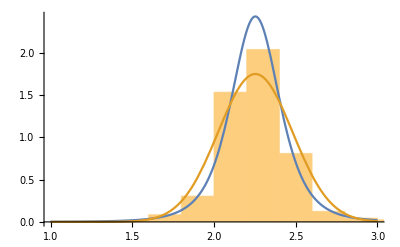

```mathematica
Show[Histogram[mm3,Automatic,"ProbabilityDensity"],Plot[{PDF[TsallisQGaussianDistribution[2.253,0.13770,1.404],x],PDF[NormalDistribution[2.253,0.2279768],x]},{x,1,3}]]
```

```mathematica
TsallisVar[μ_, β_, q_] :=Variance[TsallisQGaussianDistribution[μ,β,q]]
NormalVar[μ_, σ_]:=Variance[NormalDistribution[μ,σ]]


TsallisDrift[μ_, β_,q_]:=μ+TsallisVar[μ, β, q]/2
NormalDrift[μ_,σ_]:=μ+NormalVar[μ, σ]/2
TsallisVolatility[μ_,β_, q_]:=√TsallisVar[μ, β, q]
NormalVolatility[μ_,σ_]:=√NormalVar[μ, σ]
```

```mathematica
TsallisDrift[0.00183861,0.017202, 1.565]
```

0.0028088

```mathematica
NormalDrift[0.0018386,0.0679]
```

0.00414381

```mathematica
TsallisVolatility[0.00183861,0.017202, 1.565]
NormalVolatility[0.0018386,0.0679]
```

0.0440498

0.0679

```mathematica
TsallisVar[0.001838613476592,0.017202,1.565]
NormalVar[0.001838613476592,0.06791]
```

0.00194039

0.00461177

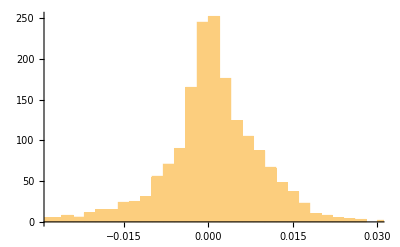

```mathematica
Histogram[return]
```

```mathematica
p =Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\SatT.csv"]];
p =p[[2]];
p = Delete[p, 1];
```

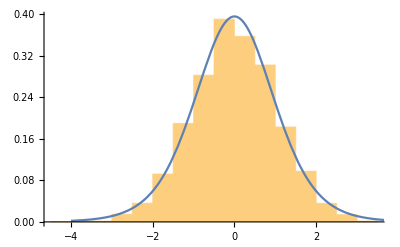

```mathematica
Show[Histogram[p,Automatic,"ProbabilityDensity"],Plot[{PDF[TsallisQGaussianDistribution[0.00039,0.931032512,1.2],x]},{x,-4,4}]]
```

```mathematica
√(1/(2*0.57682))
```

0.931033

```mathematica
Variance[TsallisQGaussianDistribution[μ,β,q]]
```

Piecewise[{{(2 β^2)/(5-3 q), q<5/3}, {∞, 5/3≤q<2}, {Indeterminate, True}}]

```mathematica
logR= Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\logR.csv"]]
logR = logR[[2]]
logR = Delete[logR,1]
```

{{,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,9773,9886,9887,9888,9889,9890,9891,9892,9893,9894,9895,9896,9897,9898,9899,9900,9901,9902,9903,9904,9905,9906,9907,9908,9909,9910,9911,9912,9913,9914,9915,9916,9917,9918,9919,9920,9921,9922,9923,9924,9925,9926,9927,9928,9929,9930,9931,9932,9933,9934,9935,9936,9937,9938,9939,9940,9941,9942,9943,9944,9945,9946,9947,9948,9949,9950,9951,9952,9953,9954,9955,9956,9957,9958,9959,9960,9961,9962,9963,9964,9965,9966,9967,9968,9969,9970,9971,9972,9973,9974,9975,9976,9977,9978,9979,9980,9981,9982,9983,9984,9985,9986,9987,9988,9989,9990,9991,9992,9993,9994,9995,9996,9997,9998,9999},1}
 |  |  |  |

{LogR,0.0130176,-0.0148429,-0.00354052,0.0054587,0.00366254,0.00637422,0.0147073,-0.00308221,0.0125325,-0.0165763,0.00846161,0.00691547,0.00416426,0.00463623,0.0100127,-0.0000469796,-0.00538793,-0.0078095,0.0123666,-0.00139287,9959,-0.00212851,0.00789123,0.0104811,0.00115236,-0.0000859796,0.00651704,0.00810629,0.00378049,0.00104893,0.0125418,-0.00251409,0.0032285,0.00870533,0.00744471,0.00822446,0.00921648,-0.00104003,0.00686851,0.00348074,0.0113657,-0.00521334}
 |  |  |  |

{0.0130176,-0.0148429,-0.00354052,0.0054587,0.00366254,0.00637422,0.0147073,-0.00308221,0.0125325,-0.0165763,0.00846161,0.00691547,0.00416426,0.00463623,0.0100127,-0.0000469796,-0.00538793,-0.0078095,0.0123666,-0.00139287,-0.0229007,9959,0.00789123,0.0104811,0.00115236,-0.0000859796,0.00651704,0.00810629,0.00378049,0.00104893,0.0125418,-0.00251409,0.0032285,0.00870533,0.00744471,0.00822446,0.00921648,-0.00104003,0.00686851,0.00348074,0.0113657,-0.00521334}
 |  |  |  |

```mathematica
logR
```

{0.0130176,-0.0148429,-0.00354052,0.0054587,0.00366254,0.00637422,0.0147073,-0.00308221,0.0125325,-0.0165763,0.00846161,0.00691547,0.00416426,0.00463623,0.0100127,-0.0000469796,-0.00538793,-0.0078095,0.0123666,-0.00139287,-0.0229007,9959,0.00789123,0.0104811,0.00115236,-0.0000859796,0.00651704,0.00810629,0.00378049,0.00104893,0.0125418,-0.00251409,0.0032285,0.00870533,0.00744471,0.00822446,0.00921648,-0.00104003,0.00686851,0.00348074,0.0113657,-0.00521334}
 |  |  |  |

```mathematica
logR[[2]]
```

{LogR,0.0130176,-0.0148429,-0.00354052,0.0054587,0.00366254,0.00637422,0.0147073,-0.00308221,0.0125325,-0.0165763,0.00846161,0.00691547,0.00416426,0.00463623,0.0100127,-0.0000469796,-0.00538793,-0.0078095,0.0123666,-0.00139287,9959,-0.00212851,0.00789123,0.0104811,0.00115236,-0.0000859796,0.00651704,0.00810629,0.00378049,0.00104893,0.0125418,-0.00251409,0.0032285,0.00870533,0.00744471,0.00822446,0.00921648,-0.00104003,0.00686851,0.00348074,0.0113657,-0.00521334}
 |  |  |  |

```mathematica
mm = profit[[2]];

mm2 = Delete[mm2,1];

FindDistributionParameters[logR,TsallisQGaussianDistribution[μ,β,q]]
```

{μ→0.00506094,β→0.00521386,q→1.48112}